# 化合物検索アルゴリズムの開発

## Program

```mathematica
SetDirectory["/home/kamano/gitsrc/Chemical-form_search_by_Eigen"]
```

/home/kamano/gitsrc/Chemical-form_search_by_Eigen

```mathematica
home="/home/kamano/"
```

/home/kamano/

```mathematica
(*home="/Users/kouamano/"*)
```

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/List_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Chemicalform_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]
```

## 技術調査

## スペクトラルグラフ理論とは

グラフの隣接行列を特性方程式問題として扱う:

インプット = > 隣接行列
アウトプット = > 固有値・固有ベクトル
パラメーター => 
	- コネクション要素の値
	- トレースの値
	- ベースの値
	- 有向/無向

```mathematica
{{a,B,B,X1},
{B,b,B,B},
{B,B,c,X2},
{X1,B,X2,d}}//MatrixForm
```

(a | B | B | X1
B | b | B | B
B | B | c | X2
X1 | B | X2 | d)

B : ベース; X : コネクション(配置が対称なら無向); {a,b,c,d} : トレース。
Xの配置のみが決まっており、あとは編集可。



```mathematica
v={1,2,3,4};e={1<->2,1<->3,1<->4};g=Graph[v,e]
```

```mathematica
(am=AdjacencyMatrix[g])//MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
(es=Eigensystem[am]);{es[[1]]//MatrixForm,es[[2]]//MatrixForm}//TableForm
```

(-√3
√3
0
0)
(-√3 | 1 | 1 | 1
√3 | 1 | 1 | 1
0 | -1 | 0 | 1
0 | -1 | 1 | 0)

```mathematica
eval=es[[1]];evec=es[[2]];
```

## 隣接行列とその固有値・固有ベクトル(を求めるアルゴリズム)の一般的な性質

固有値はノルムの大きい順に求まる

固有値の合計は変化しない

固有ベクトルのノルムは1となる(Mathematicaではそうならない)

行・列を同じオーダーで入れ替えても固有値は変化しない、ただし固有ベクトルの要素の順は変更される

```mathematica
Eigenvalues[matReOrder[AdjacencyMatrix[g]//Normal,{3,2,4,1}]]
```

{-√3,√3,0,0}

## 隣接行列においてコネクションの強度がその固有値・固有ベクトルに及ぼす影響

```mathematica
ex1={{4,0,0,0},
{0,3,0,0},
{0,0,2,0},
{0,0,0,1}
}
```

{{4,0,0,0},{0,3,0,0},{0,0,2,0},{0,0,0,1}}

```mathematica
nex1=nEingensystem[ex1]
```

{{4,3,2,1},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}}

コネクションの強度が弱ければ、固有値列(パワースペクトル)への影響が少ない。

```mathematica
ex2={{4,0,0,0.1},
{0,3,0,0},
{0,0,2,0},
{0.1,0,0,1}
}
```

{{4,0,0,0.1},{0,3,0,0},{0,0,2,0},{0.1,0,0,1}}

```mathematica
nex2=nEingensystem[ex2]
```

{{4.00333,3.,2.,0.99667},{{-0.999446,0.,0.,-0.0332779},{0.,1.,0.,0.},{0.,0.,-1.,0.},{-0.0332779,0.,0.,0.999446}}}

```mathematica
Tr[nex2[[1]]]
```

10.

```mathematica
ex3={{4,0,0,1},
{0,3,0,0},
{0,0,2,0},
{1,0,0,1}
}
```

{{4,0,0,1},{0,3,0,0},{0,0,2,0},{1,0,0,1}}

```mathematica
nex3=nEingensystem[ex3]//N
```

{{4.30278,3.,2.,0.697224},{{0.957092,0.,0.,0.289784},{0.,1.,0.,0.},{0.,0.,1.,0.},{-0.289784,0.,0.,0.957092}}}

```mathematica
Tr[nex3[[1]]]
```

10.

```mathematica
ex4={{4,0,0,10},
{0,3,0,0},
{0,0,2,0},
{10,0,0,1}
}
```

{{4,0,0,10},{0,3,0,0},{0,0,2,0},{10,0,0,1}}

```mathematica
nex4=nEingensystem[ex4]//N
```

{{12.6119,-7.61187,3.,2.},{{0.75774,0.,0.,0.652556},{-0.652556,0.,0.,0.75774},{0.,1.,0.,0.},{0.,0.,1.,0.}}}

```mathematica
ex5={{4,0,0,-10},
{0,3,0,0},
{0,0,2,0},
{-10,0,0,1}
}
```

{{4,0,0,-10},{0,3,0,0},{0,0,2,0},{-10,0,0,1}}

```mathematica
nex5=nEingensystem[ex5]//N
```

{{12.6119,-7.61187,3.,2.},{{-0.75774,0.,0.,0.652556},{0.652556,0.,0.,0.75774},{0.,1.,0.,0.},{0.,0.,1.,0.}}}

```mathematica
Tr[nex5[[1]]]
```

10.

## スペクトラルグラフ理論を応用した化合物検索の先行事例

Milan Randic. 
On Characterization of Molecular Branching. 
Journal of The American Chemical Society. 
Vol.97, Num.23, p .6609. 
1975.

Frank R. Burden. 
Molecular Identification Number for Substructure Searches.
Journal of Chemical Information and Computer Sciences. 
Vol. 29, p.225. 
1989.

いずれも、系統の近い分子のマッチングに有効。

## アルゴリズム提案

本質的に、あらゆる系統の単独分子同士のマッチングに応用可能な方法を目指す。

## 技術コンセプト

固有値列 (パワースペクトル) のみを利用する(固有ベクトルの差は無視する )

対角要素に原子番号を付与することにより原子集合を構成・区別する

原子番号(構成原子の種類)とコネクションの強度を設定することによりうまく(目的別に)分子を区別できないか？

ひとまず2分子マッチを前提とする

双方の共通な原子集合を構成し、差異はコネクションを利用する

## アルゴリズム定義

### Pseudo Code

0   (***** Pseudo Code *****)
1   Compound A
2   Compound B
3
4   AC = AtomCount (A, B)
5
6   BM[A] = AddBond (AC, A, tr = "Atomic number", bond = "Order", bg = 0)
7   BM[B] = AddBond (AC, B, tr = "Atomic number", bond = "Order", bg = 0)
8 
9    EVL[A] = Normalize (Eigenvalues (BM[A]))
10 EVL[B] = Normalize (Eigenvalues (BM[B]))
11
12  { IDX[A, B] = Inner (EVL[A], EVL[B])
13  OR
14  IDX[A, B] = Dist (EVL[A], EVL[B]) }
15  (* Parameters: tr,bond, bg. *)

### Work Flow

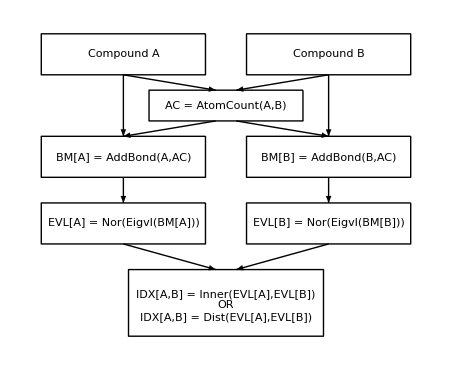

## 実装例

## Clustering of Amino Acids

### Data

```mathematica
cc=ChemicalData["Classes"];
```

```mathematica
AA=ChemicalData["AminoAcids"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
numAA = Length[AA]
```

20

```mathematica
AAName=Map[ChemicalData[#,"Name"]&,AA]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
AAFig=Map[ChemicalData[#]&,AA];
```

```mathematica
AAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, AAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(AAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,AA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{«1»},«17»,{«1»}}

```mathematica
(AAVT=Map[ChemicalData[#,"VertexTypes"]&,AA])//Short
```

{{C,C,N,O,O,H,H,H,H,H},«18»,{C,C,C,C,C,C,N,«13»,C,H,H,H,O,O,H}}

```mathematica
(elmAAAdjMat=Table[elementAdjMat[AAAdjMat[[n]],AAVT[[n]]],{n,Length[AAAdjMat]}])//Length
```

20

```mathematica
(AADmat=Outer[eigenSpectrumDistance,elmAAAdjMat,elmAAAdjMat,1])//Dimensions
```

{20,20}

### Clustering

Candidate:

```mathematica
ag["A"]=DirectAgglomerate[AADmat,Linkage->"Average"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[1,Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],6,0.798298,3,1],1.31674,1,4],Cluster[Cluster[Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.5617,2,1],0.704903,1,3],Cluster[16,18,0.92273,1,1],1.56884,4,2],Cluster[Cluster[4,Cluster[Cluster[5,15,0.466146,1,1],Cluster[8,9,0.522399,1,1],0.835355,2,2],0.928711,1,4],13,1.04394,5,1],1.81684,6,6],2.22909,5,12],Cluster[20,Cluster[19,17,0.588454,1,1],1.63161,1,2],4.08975,17,3]

```mathematica
ag["WA"]=DirectAgglomerate[AADmat,Linkage->"WeightedAverage"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],0.994135,1,3],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.844398,2,1],0.927675,1,3],Cluster[Cluster[5,15,0.466146,1,1],6,0.819333,2,1],1.08802,4,3],1.58344,4,7],Cluster[Cluster[18,16,0.92273,1,1],Cluster[Cluster[11,Cluster[14,10,0.468095,1,1],0.5617,1,2],12,0.659033,3,1],1.65253,2,4],2.03674,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.63161,2,1],3.73837,17,3]

```mathematica
ag["W"]=DirectAgglomerate[AADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],4.67907,5,6],Cluster[Cluster[16,18,0.92273,1,1],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.592902,2,1],0.723301,1,3],3.19682,2,4],7.56004,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.97933,2,1],12.9788,17,3]

```mathematica
ag["C"]=DirectAgglomerate[AADmat,Linkage->"Centroid"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[1,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.596282,2,1],6,0.645681,3,1],Cluster[5,15,0.466146,1,1],0.646992,4,2],Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.713799,2,1],0.681986,1,3],0.729913,6,4],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.444676,2,1],0.482201,1,3],1.02204,10,4],Cluster[16,18,0.92273,1,1],1.27935,14,2],1.46387,1,16],Cluster[20,Cluster[19,17,0.588454,1,1],1.4845,1,2],2.54486,17,3]

### Selection

#### Method["A"]

```mathematica
meth="A"
```

A

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,7.20962,7.42148,7.63739,7.99359,8.70209,9.5186,10.3446,11.162,11.9413,12.776,13.6574,14.5075,15.4058,16.2942,17.2057,18.1269,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{4.08975,2.22909,1.81684,1.63161,1.56884,1.31674,1.04394,0.928711,0.92273,0.835355,0.798298,0.704903,0.669325,0.588454,0.5617,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{4.08975,20.},{2.22909,7.11861},{1.81684,7.20962},{1.63161,7.42148},{1.56884,7.63739},{1.31674,7.99359},{1.04394,8.70209},{0.928711,9.5186},{0.92273,10.3446},{0.835355,11.162},{0.798298,11.9413},{0.704903,12.776},{0.669325,13.6574},{0.588454,14.5075},{0.5617,15.4058},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.403983

#### Method["WA"]

```mathematica
meth="WA"
```

WA

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,7.18004,6.96998,7.26336,7.97071,8.7945,9.53531,10.3385,11.1561,11.9611,12.776,13.6236,14.5075,15.4058,16.2942,17.2057,18.1269,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{3.73837,2.03674,1.65253,1.63161,1.58344,1.08802,0.994135,0.927675,0.92273,0.844398,0.819333,0.669325,0.659033,0.588454,0.5617,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{3.73837,20.},{2.03674,7.11861},{1.65253,7.18004},{1.63161,6.96998},{1.58344,7.26336},{1.08802,7.97071},{0.994135,8.7945},{0.927675,9.53531},{0.92273,10.3385},{0.844398,11.1561},{0.819333,11.9611},{0.669325,12.776},{0.659033,13.6236},{0.588454,14.5075},{0.5617,15.4058},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.397261

#### Method["W"]

```mathematica
meth="W"
```

W

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[ag[meth],n],{n,numAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[AADmat,agspFL[meth][[n]]],{n,numAA}]
```

{20.,7.11861,7.18004,7.42148,7.57266,7.99359,8.70209,9.51355,10.2962,11.1119,11.9181,12.7504,13.6322,14.5075,15.3948,16.2942,17.2057,18.1269,19.0488,20.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[ag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{12.9788,7.56004,4.67907,3.19682,1.97933,1.43447,1.43198,1.05103,1.02298,0.951732,0.92273,0.723301,0.71254,0.592902,0.588454,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
cls[meth]=Append[Table[Cases[ag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numAA-1}],numAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{12.9788,20.},{7.56004,7.11861},{4.67907,7.18004},{3.19682,7.42148},{1.97933,7.57266},{1.43447,7.99359},{1.43198,8.70209},{1.05103,9.51355},{1.02298,10.2962},{0.951732,11.1119},{0.92273,11.9181},{0.723301,12.7504},{0.71254,13.6322},{0.592902,14.5075},{0.588454,15.3948},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.491365

### Plot

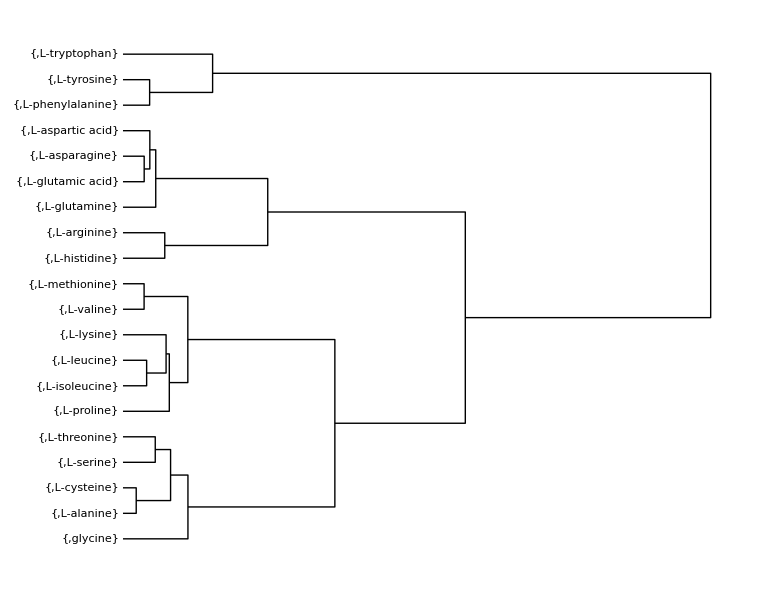

```mathematica
DendrogramPlot[ag["W"],LeafLabels->({AAFig45[[#]],AAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

## Clustering of Amino Acids + Lipids

Getting the information of lipids

```mathematica
(LP=ChemicalData["Lipids"])//Short
```

{heptane-1-13 C,heptane-d 16,octanoic acid-1-13 C,octanoic acid-1,2,3,4-13 C4,2-keto-4-methylpentanoic acid-1-13 csodium salt,octanoic-d 15 acid,sodium octanoate-1-13 C,menadione,decanoic acid-1-13 C,decanoic-d 19 acid,lauric acid-12-13 C,lauric acid-1-13 C,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-1-13 C,myristic acid-1,2-13 C2,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-1-13 C,palmitic acid-2-13 C,palmitic acid-1,2-13 C2,palmitic acid-2,2-d 2,palmitic acid-13 C16,oleic acid-1-13 C,stearic acid-1-13 C,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-1-13 C,potassium palmitate-2,2-d 2,oleic acid-13 C18,stearic-d 35 acid,octanoic acid-7-13 C,dodecylphosphorylcholine-d 38,α-tocopherol,glyceryl tri(octanoate-1-13 C),glyceryl-2-13 ctripalmitate,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
(lipidsName=Map[ChemicalData[#,"Name"]&,LP])//Short
```

{heptane-1-13 C,heptane-d 16,«37»,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
isoQ=Table[StringMatchQ[lipidsName[[n]],RegularExpression[".*13 {0,1}[Cc].*"]],{n,Length[lipidsName]}];
```

```mathematica
nonIsoPos=Position[isoQ,False]
```

{{2},{6},{8},{10},{13},{14},{15},{18},{19},{20},{24},{28},{29},{30},{32},{34},{36},{37}}

```mathematica
lipidsNonIso=LP[[nonIsoPos//Flatten]]
```

{heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

Merging and Clustering

```mathematica
LPAA=Flatten[{AA,lipidsNonIso}]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
numLPAA=Length[LPAA]
```

38

```mathematica
(LPAAName=Map[ChemicalData[#,"Name"]&,LPAA])//Short
```

{glycine,L-alanine,L-serine,L-proline,«31»,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
(LPAAFig=Map[ChemicalData[#]&,LPAA])//Length
```

38

```mathematica
LPAAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, LPAAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(LPAAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,LPAA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},«36»,{{«1»},«80»}}

```mathematica
(LPAAVT=Map[ChemicalData[#,"VertexTypes"]&,LPAA])//Short
```

{{C,C,N,O,O,H,H,H,H,H},«36»,{O,O,C,C,C,C,C,«67»,H,H,H,H,H,H,H}}

```mathematica
(elmLPAAAdjMat=Table[elementAdjMat[LPAAAdjMat[[n]],LPAAVT[[n]]],{n,Length[LPAAAdjMat]}])//Length
```

38

```mathematica
(LPAADmat=Outer[eigenSpectrumDistance,elmLPAAAdjMat,elmLPAAAdjMat,1])//Dimensions
```

{38,38}

```mathematica
lpaaag["W"]=DirectAgglomerate[LPAADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],Cluster[21,Cluster[22,24,1.00798,1,1],2.20387,1,2],3.62661,6,3],6.28158,5,9],Cluster[Cluster[16,18,0.92273,1,1],Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.592902,2,1],12,0.723301,3,1],3.19682,2,4],7.67005,14,6],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[34,31,0.,1,1],35,0.244229,2,1],Cluster[Cluster[30,28,0.,1,1],29,0.774995,2,1],2.23878,3,3],37,2.3346,6,1],Cluster[33,Cluster[32,36,0.,1,1],0.,1,2],3.68258,7,3],Cluster[27,Cluster[25,26,0.,1,1],0.,1,2],5.51745,10,3],Cluster[Cluster[Cluster[17,19,0.588454,1,1],Cluster[20,23,0.961533,1,1],2.31466,2,2],38,6.97161,4,1],10.7161,13,5],36.6737,20,18]

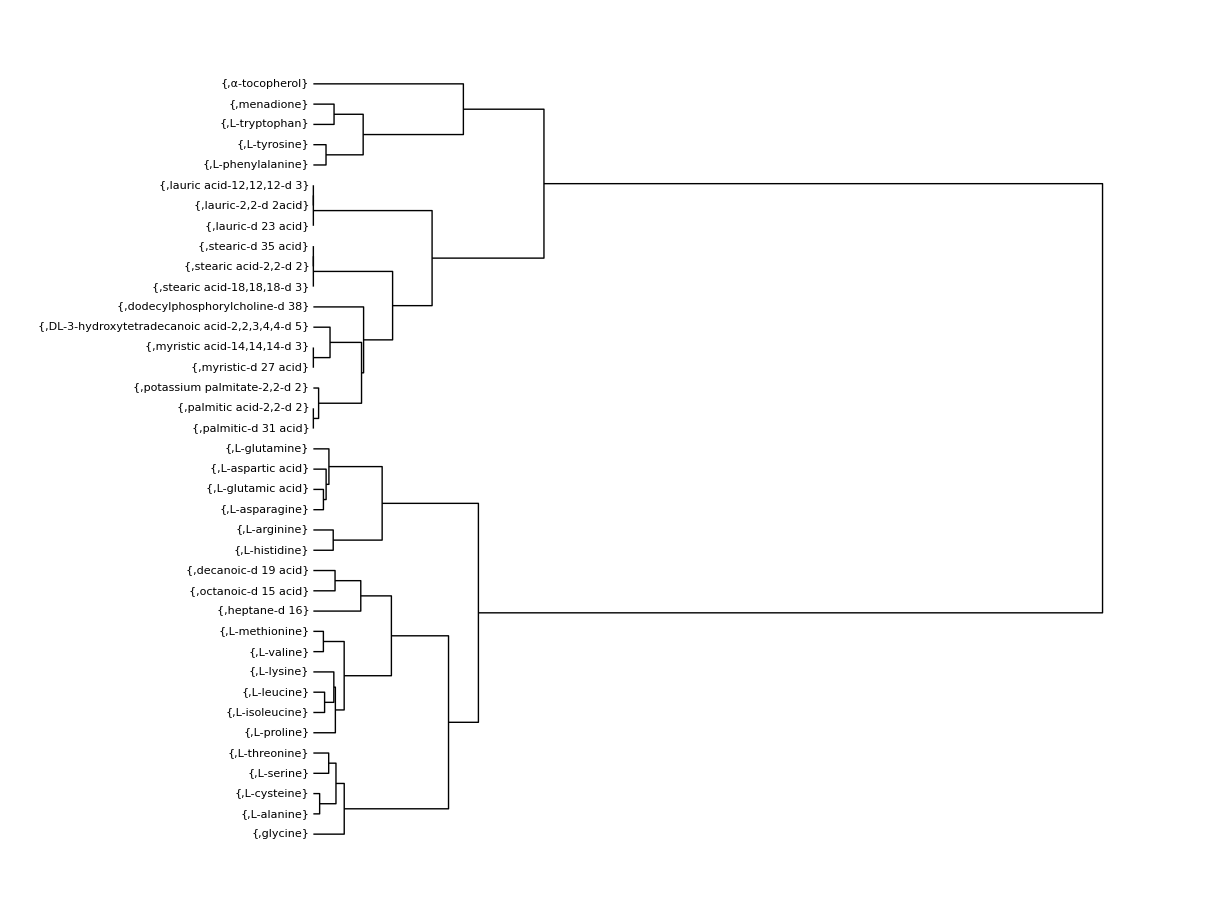

```mathematica
DendrogramPlot[lpaaag["W"],LeafLabels->({LPAAFig45[[#]],LPAAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

## Clustering of Amino Acids + Lipids (2)

### Data

Getting the information of lipids

```mathematica
(LP=ChemicalData["Lipids"])//Short
```

{heptane-1-13 C,heptane-d 16,octanoic acid-1-13 C,octanoic acid-1,2,3,4-13 C4,2-keto-4-methylpentanoic acid-1-13 csodium salt,octanoic-d 15 acid,sodium octanoate-1-13 C,menadione,decanoic acid-1-13 C,decanoic-d 19 acid,lauric acid-12-13 C,lauric acid-1-13 C,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-1-13 C,myristic acid-1,2-13 C2,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-1-13 C,palmitic acid-2-13 C,palmitic acid-1,2-13 C2,palmitic acid-2,2-d 2,palmitic acid-13 C16,oleic acid-1-13 C,stearic acid-1-13 C,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-1-13 C,potassium palmitate-2,2-d 2,oleic acid-13 C18,stearic-d 35 acid,octanoic acid-7-13 C,dodecylphosphorylcholine-d 38,α-tocopherol,glyceryl tri(octanoate-1-13 C),glyceryl-2-13 ctripalmitate,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
(lipidsName=Map[ChemicalData[#,"Name"]&,LP])//Short
```

{heptane-1-13 C,heptane-d 16,«37»,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
isoQ=Table[StringMatchQ[lipidsName[[n]],RegularExpression[".*13 {0,1}[Cc].*"]],{n,Length[lipidsName]}];
```

```mathematica
nonIsoPos=Position[isoQ,False]
```

{{2},{6},{8},{10},{13},{14},{15},{18},{19},{20},{24},{28},{29},{30},{32},{34},{36},{37}}

```mathematica
lipidsNonIso=LP[[nonIsoPos//Flatten]]
```

{heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

Merging and Clustering

```mathematica
(LPAA=Flatten[{AA,lipidsNonIso}])//Short
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
numLPAA=Length[LPAA]
```

38

```mathematica
(LPAAName=Map[ChemicalData[#,"Name"]&,LPAA])//Short
```

{glycine,L-alanine,L-serine,«32»,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
(LPAAFig=Map[ChemicalData[#]&,LPAA])//Length
```

38

```mathematica
LPAAFig45=Map[Graphics[#[[1]] , ImageSize->{45,45}]&, LPAAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(LPAAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,LPAA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},«36»,{«1»}}

```mathematica
(LPAAVT=Map[ChemicalData[#,"VertexTypes"]&,LPAA])//Short
```

{{C,C,N,O,O,H,H,H,H,H},«36»,{O,O,C,C,C,C,C,«67»,H,H,H,H,H,H,H}}

```mathematica
(elmLPAAAdjMat=Table[elementAdjMat[LPAAAdjMat[[n]],LPAAVT[[n]]],{n,Length[LPAAAdjMat]}])//Length
```

38

```mathematica
(repElmLPAAAdjMat=Map[repConnection[#,2#&,0]&,elmLPAAAdjMat,{1}])//Short
```

{{{6,2,2,0,0,0,0,0,2,2},{2,6,0,2,4,0,0,0,0,0},«6»,{2,0,0,0,0,0,0,0,1,0},{2,0,0,0,0,0,0,0,0,1}},«36»,{«1»}}

```mathematica
(LPAADmat=Outer[eigenSpectrumDistance,repElmLPAAAdjMat,elmLPAAAdjMat,1])//Dimensions
```

{38,38}

### Clustering

```mathematica
lpaaag["A"]=DirectAgglomerate[LPAADmat,Linkage->"Average"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,3.89436,2,1],2,4.08396,3,1],6,4.15304,4,1],12,4.34877,5,1],Cluster[7,10,3.71722,1,1],4.48052,6,2],8,4.75874,8,1],Cluster[5,14,4.92509,1,1],5.00227,9,2],Cluster[Cluster[4,16,4.32732,1,1],13,4.97064,2,1],5.14284,11,3],Cluster[9,19,5.00492,1,1],5.24319,14,2],Cluster[15,18,4.59368,1,1],5.45755,16,2],23,5.60145,18,1],17,6.06152,19,1],20,6.6536,20,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[35,38,7.58233,1,1],36,7.84804,2,1],Cluster[Cluster[Cluster[Cluster[25,31,6.88481,1,1],Cluster[Cluster[26,Cluster[Cluster[29,Cluster[22,Cluster[24,21,4.62,1,1],5.25986,1,2],5.62261,1,3],27,6.20158,4,1],6.6522,1,5],28,6.84029,6,1],7.01368,2,7],30,7.19591,9,1],33,7.30753,10,1],7.88622,3,11],34,7.98177,14,1],37,8.2816,15,1],32,8.6344,16,1],9.11363,21,17]

```mathematica
lpaaag["WA"]=DirectAgglomerate[LPAADmat,Linkage->"WeightedAverage"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,3.89436,2,1],2,4.06901,3,1],6,4.10547,4,1],Cluster[7,10,3.71722,1,1],4.32247,5,2],12,4.36208,7,1],14,4.54247,8,1],8,4.75684,9,1],5,4.78994,10,1],Cluster[4,16,4.32732,1,1],4.83382,11,2],9,4.93351,13,1],13,5.11052,14,1],Cluster[15,18,4.59368,1,1],5.19114,15,2],19,5.28783,17,1],23,5.56635,18,1],17,5.61809,19,1],20,5.92507,20,1],Cluster[Cluster[26,Cluster[27,Cluster[Cluster[29,Cluster[Cluster[24,21,4.62,1,1],22,5.25986,2,1],5.5712,1,3],25,5.90316,4,1],6.14309,1,5],6.30305,1,6],28,6.4827,7,1],6.53326,21,8],30,6.65823,29,1],31,6.82181,30,1],34,6.86311,31,1],35,6.91736,32,1],36,7.07628,33,1],32,7.17141,34,1],33,7.21011,35,1],37,7.30756,36,1],38,7.68311,37,1]

```mathematica
lpaaag["W"]=DirectAgglomerate[LPAADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[1,3,3.62353,1,1],11,3.98463,2,1],Cluster[Cluster[2,6,4.11048,1,1],12,4.28188,2,1],4.56724,3,3],5,4.91669,6,1],8,5.13273,7,1],Cluster[Cluster[7,10,3.71722,1,1],14,4.73625,2,1],5.39631,8,3],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[4,16,4.32732,1,1],13,5.18508,2,1],23,5.71194,3,1],Cluster[9,19,5.00492,1,1],5.89862,4,2],17,6.01637,6,1],Cluster[Cluster[15,18,4.59368,1,1],20,6.07126,2,1],7.07606,7,3],7.22711,11,10],Cluster[Cluster[Cluster[33,Cluster[Cluster[Cluster[31,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[29,Cluster[Cluster[21,24,4.62,1,1],22,5.47315,2,1],5.83352,1,3],27,6.25973,4,1],25,6.54076,5,1],26,6.70135,6,1],28,6.91617,7,1],30,7.128,8,1],34,7.20198,9,1],7.36563,1,10],36,7.5353,11,1],32,7.81978,12,1],7.92065,1,13],37,8.26097,14,1],Cluster[38,35,7.58233,1,1],8.44115,15,2],20.6334,21,17]

### Selection

#### Method["A"]

```mathematica
meth="A"
```

A

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,33.4687,19.1021,15.7137,14.7103,17.278,16.1808,14.7821,15.2724,15.9064,17.425,17.2399,17.9126,18.6794,19.3951,20.0744,20.9389,21.5143,22.3156,23.8142,24.4154,25.8945,27.5922,27.8648,29.2503,29.8816,30.2934,31.1666,31.5435,31.9675,33.2498,34.0561,34.4979,35.3458,36.1657,36.8424,37.3807,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{9.11363,8.6344,8.2816,7.98177,7.88622,7.84804,7.58233,7.30753,7.19591,7.01368,6.88481,6.84029,6.6536,6.6522,6.20158,6.06152,5.62261,5.60145,5.45755,5.25986,5.24319,5.14284,5.00492,5.00227,4.97064,4.92509,4.75874,4.62,4.59368,4.48052,4.34877,4.32732,4.15304,4.08396,3.89436,3.71722,3.62353,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{9.11363,38.},{8.6344,33.4687},{8.2816,19.1021},{7.98177,15.7137},{7.88622,14.7103},{7.84804,17.278},{7.58233,16.1808},{7.30753,14.7821},{7.19591,15.2724},{7.01368,15.9064},{6.88481,17.425},{6.84029,17.2399},{6.6536,17.9126},{6.6522,18.6794},{6.20158,19.3951},{6.06152,20.0744},{5.62261,20.9389},{5.60145,21.5143},{5.45755,22.3156},{5.25986,23.8142},{5.24319,24.4154},{5.14284,25.8945},{5.00492,27.5922},{5.00227,27.8648},{4.97064,29.2503},{4.92509,29.8816},{4.75874,30.2934},{4.62,31.1666},{4.59368,31.5435},{4.48052,31.9675},{4.34877,33.2498},{4.32732,34.0561},{4.15304,34.4979},{4.08396,35.3458},{3.89436,36.1657},{3.71722,36.8424},{3.62353,37.3807},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.223491

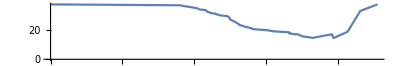

```mathematica
ListPlot[pt["A"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["WA"]

```mathematica
meth="WA"
```

WA

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,11.5325,9.46621,9.31537,9.69708,10.2932,11.0184,11.7981,12.6111,13.4657,16.5265,17.2009,17.9126,18.6095,19.3951,20.0744,20.9389,21.5143,22.3156,23.1732,23.7891,25.2606,26.1824,27.1017,28.5002,29.4117,30.2968,30.6683,31.088,31.9675,32.8214,33.2664,34.4979,35.3458,36.1657,36.8424,37.3807,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{7.68311,7.30756,7.21011,7.17141,7.07628,6.91736,6.86311,6.82181,6.65823,6.53326,6.4827,6.30305,6.14309,5.92507,5.90316,5.61809,5.5712,5.56635,5.28783,5.25986,5.19114,5.11052,4.93351,4.83382,4.78994,4.75684,4.62,4.59368,4.54247,4.36208,4.32732,4.32247,4.10547,4.06901,3.89436,3.71722,3.62353,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{7.68311,38.},{7.30756,11.5325},{7.21011,9.46621},{7.17141,9.31537},{7.07628,9.69708},{6.91736,10.2932},{6.86311,11.0184},{6.82181,11.7981},{6.65823,12.6111},{6.53326,13.4657},{6.4827,16.5265},{6.30305,17.2009},{6.14309,17.9126},{5.92507,18.6095},{5.90316,19.3951},{5.61809,20.0744},{5.5712,20.9389},{5.56635,21.5143},{5.28783,22.3156},{5.25986,23.1732},{5.19114,23.7891},{5.11052,25.2606},{4.93351,26.1824},{4.83382,27.1017},{4.78994,28.5002},{4.75684,29.4117},{4.62,30.2968},{4.59368,30.6683},{4.54247,31.088},{4.36208,31.9675},{4.32732,32.8214},{4.32247,33.2664},{4.10547,34.4979},{4.06901,35.3458},{3.89436,36.1657},{3.71722,36.8424},{3.62353,37.3807},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.21765

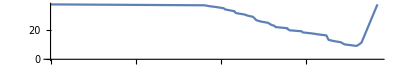

```mathematica
ListPlot[pt["WA"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

#### Method["W"]

```mathematica
meth="W"
```

W

Validation:

```mathematica
Map[Length,(agsp[meth]=Table[ClusterSplit[lpaaag[meth],n],{n,numLPAA}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
agspFL[meth]=Map[ClusterFlatten,agsp[meth],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps[meth]=Table[piDMG[LPAADmat,agspFL[meth][[n]]],{n,numLPAA}]
```

{38.,33.4687,24.5304,18.8997,16.9387,16.2511,14.3498,14.7378,15.2724,18.2214,18.7304,19.326,21.2778,21.8753,22.5191,23.1524,23.7543,23.9848,24.7361,26.022,26.559,27.0097,27.5922,29.2134,29.8231,30.6691,30.9548,31.812,32.4572,32.8299,33.2498,34.5216,34.955,35.6075,36.1657,36.8424,37.3807,38.}

:Agglomerated distance:

```mathematica
ad[meth]=Append[Sort[Map[#[[3]]&,Cases[lpaaag[meth],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{20.6334,8.44115,8.26097,7.92065,7.81978,7.58233,7.5353,7.36563,7.22711,7.20198,7.128,7.07606,6.91617,6.70135,6.54076,6.25973,6.07126,6.01637,5.89862,5.83352,5.71194,5.47315,5.39631,5.18508,5.13273,5.00492,4.91669,4.73625,4.62,4.59368,4.56724,4.32732,4.28188,4.11048,3.98463,3.71722,3.62353,0}

```mathematica
cls[meth]=Append[Table[Cases[lpaaag[meth],Cluster[_,_,x_,_,_]/;x≤ad[meth][[1]]&&x≥ad[meth][[n]],{0,Infinity}]//Length,{n,numLPAA-1}],numLPAA]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

:Validation point:

```mathematica
pt[meth]=Transpose[{ad[meth],cvisteps[meth]}]
```

{{20.6334,38.},{8.44115,33.4687},{8.26097,24.5304},{7.92065,18.8997},{7.81978,16.9387},{7.58233,16.2511},{7.5353,14.3498},{7.36563,14.7378},{7.22711,15.2724},{7.20198,18.2214},{7.128,18.7304},{7.07606,19.326},{6.91617,21.2778},{6.70135,21.8753},{6.54076,22.5191},{6.25973,23.1524},{6.07126,23.7543},{6.01637,23.9848},{5.89862,24.7361},{5.83352,26.022},{5.71194,26.559},{5.47315,27.0097},{5.39631,27.5922},{5.18508,29.2134},{5.13273,29.8231},{5.00492,30.6691},{4.91669,30.9548},{4.73625,31.812},{4.62,32.4572},{4.59368,32.8299},{4.56724,33.2498},{4.32732,34.5216},{4.28188,34.955},{4.11048,35.6075},{3.98463,36.1657},{3.71722,36.8424},{3.62353,37.3807},{0,38.}}

:Total validation:

```mathematica
dAreaRatio[pt[meth]]
```

0.113742

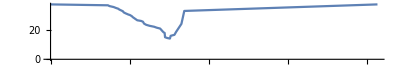

```mathematica
ListPlot[pt["W"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

### Plot

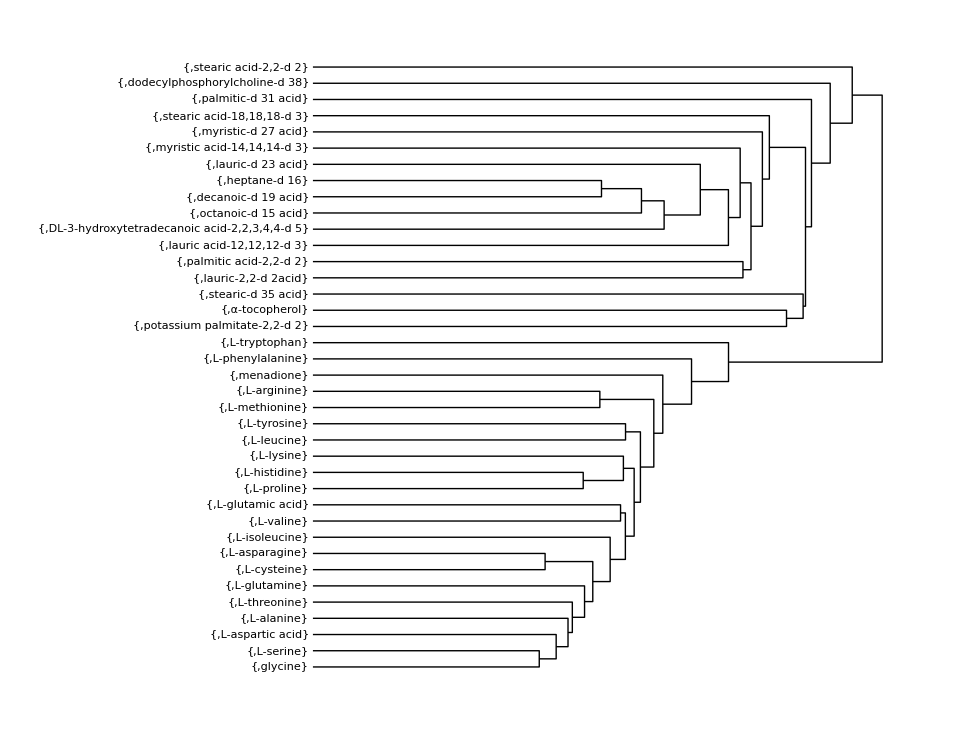

```mathematica
DendrogramPlot[lpaaag["A"],LeafLabels->({LPAAFig45[[#]],LPAAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

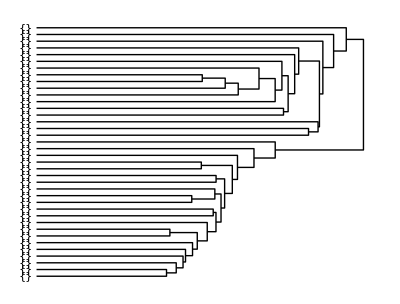

```mathematica
dp3=DendrogramPlot[lpaaag["A"],LeafLabels->({LPAAFig45[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

## Chart

### Definitions

```mathematica
box[{x1_,y1_},{x2_,y2_}]:=Line[{{x1,y1},{x1,y2},{x2,y2},{x2,y1},{x1,y1}}]
```

### Object

```mathematica
coA={-1,0};coB={1,0}
```

{1,0}

Row1

```mathematica
bA=box[coA+{0,-0.75}+{0.8,0.2},coA+{0,-0.75}+{-0.8,-0.2}]
```

Line[{{-0.2,-0.55},{-0.2,-0.95},{-1.8,-0.95},{-1.8,-0.55},{-0.2,-0.55}}]

```mathematica
bB=box[coB+{0,-0.75}+{0.8,0.2},coB+{0,-0.75}+{-0.8,-0.2}]
```

Line[{{1.8,-0.55},{1.8,-0.95},{0.2,-0.95},{0.2,-0.55},{1.8,-0.55}}]

```mathematica
tA=Text["Compound A",coA+{0,-0.75}]
```

Text[Compound A,{-1,-0.75}]

```mathematica
tB=Text["Compound B",coB+{0,-0.75}]
```

Text[Compound B,{1,-0.75}]

Row2(not used)

```mathematica
bA2=box[coA+{0.8,0.2}+{0,-0.75},coA+{-0.8,-0.2}+{0,-0.75}]
```

Line[{{-0.2,-0.55},{-0.2,-0.95},{-1.8,-0.95},{-1.8,-0.55},{-0.2,-0.55}}]

```mathematica
bB2=box[coB+{0.8,0.2}+{0,-0.75},coB+{-0.8,-0.2}+{0,-0.75}]
```

Line[{{1.8,-0.55},{1.8,-0.95},{0.2,-0.95},{0.2,-0.55},{1.8,-0.55}}]

```mathematica
tA2=Text["CA[A] = CountAtoms(A)",coA+{0,-0.75}]
```

Text[CA[A] = CountAtoms(A),{-1,-0.75}]

```mathematica
tB2=Text["CA[B] = CountAtoms(B)",coB+{0,-0.75}]
```

Text[CA[B] = CountAtoms(B),{1,-0.75}]

Row3

```mathematica
bmc=box[{0,-1.25}+{0.75,0.15},{0,-1.25}+{-0.75,-0.15}]
```

Line[{{0.75,-1.1},{0.75,-1.4},{-0.75,-1.4},{-0.75,-1.1},{0.75,-1.1}}]

```mathematica
mc=Text["AC = AtomCount(A,B)",{0,-1.25}]
```

Text[AC = AtomCount(A,B),{0,-1.25}]

Row4

```mathematica
bA3=box[coA+{0.8,0.2}+{0,-1.75},coA+{-0.8,-0.2}+{0,-1.75}]
```

Line[{{-0.2,-1.55},{-0.2,-1.95},{-1.8,-1.95},{-1.8,-1.55},{-0.2,-1.55}}]

```mathematica
bB3=box[coB+{0.8,0.2}+{0,-1.75},coB+{-0.8,-0.2}+{0,-1.75}]
```

Line[{{1.8,-1.55},{1.8,-1.95},{0.2,-1.95},{0.2,-1.55},{1.8,-1.55}}]

```mathematica
tA3=Text["BM[A] = AddBond(A,AC)",coA+{0,-1.75}]
```

Text[BM[A] = AddBond(A,AC),{-1,-1.75}]

```mathematica
tB3=Text["BM[B] = AddBond(B,AC)",coB+{0,-1.75}]
```

Text[BM[B] = AddBond(B,AC),{1,-1.75}]

Row5

```mathematica
bA4=box[coA+{0.8,0.2}+{0,-2.4},coA+{-0.8,-0.2}+{0,-2.4}]
```

Line[{{-0.2,-2.2},{-0.2,-2.6},{-1.8,-2.6},{-1.8,-2.2},{-0.2,-2.2}}]

```mathematica
bB4=box[coB+{0.8,0.2}+{0,-2.4},coB+{-0.8,-0.2}+{0,-2.4}]
```

Line[{{1.8,-2.2},{1.8,-2.6},{0.2,-2.6},{0.2,-2.2},{1.8,-2.2}}]

```mathematica
tA4=Text["EVL[A] = Nor(Eigvl(BM[A]))",coA+{0,-2.4}]
```

Text[EVL[A] = Nor(Eigvl(BM[A])),{-1,-2.4}]

```mathematica
tB4=Text["EVL[B] = Nor(Eigvl(BM[B]))",coB+{0,-2.4}]
```

Text[EVL[B] = Nor(Eigvl(BM[B])),{1,-2.4}]

Row6

```mathematica
bidx=box[{0,-3}+{0.95,0.15},{0,-3}+{-0.95,-0.5}]
```

Line[{{0.95,-2.85},{0.95,-3.5},{-0.95,-3.5},{-0.95,-2.85},{0.95,-2.85}}]

```mathematica
tidx=Text["IDX[A,B] = Inner(EVL[A],EVL[B])
OR
IDX[A,B] = Dist(EVL[A],EVL[B])",{0,-3.2}]
```

Text[IDX[A,B] = Inner(EVL[A],EVL[B])
OR
IDX[A,B] = Dist(EVL[A],EVL[B]),{0,-3.2}]

Arrow

```mathematica
ar={Arrow[{coA+{0,-0.95},coA+{0,-1.55}}],Arrow[{coB+{0,-0.95},coB+{0,-1.55}}],
Arrow[{coA+{0,-0.95},coA+{0.9,-1.1}}],Arrow[{coB+{0,-0.95},coB+{-0.9,-1.1}}],
Arrow[{coA+{0.9,-1.4},coA+{0,-1.55}}],Arrow[{coB+{-0.9,-1.4},coB+{0,-1.55}}],
Arrow[{coA+{0,-1.95},coA+{0,-2.2}}],Arrow[{coB+{0,-1.95},coB+{0,-2.2}}],
Arrow[{coA+{0,-2.6},coA+{0.9,-2.85}}],Arrow[{coB+{0,-2.6},coB+{-0.9,-2.85}}]
}
```

{Arrow[{{-1,-0.95},{-1,-1.55}}],Arrow[{{1,-0.95},{1,-1.55}}],Arrow[{{-1,-0.95},{-0.1,-1.1}}],Arrow[{{1,-0.95},{0.1,-1.1}}],Arrow[{{-0.1,-1.4},{-1,-1.55}}],Arrow[{{0.1,-1.4},{1,-1.55}}],Arrow[{{-1,-1.95},{-1,-2.2}}],Arrow[{{1,-1.95},{1,-2.2}}],Arrow[{{-1,-2.6},{-0.1,-2.85}}],Arrow[{{1,-2.6},{0.1,-2.85}}]}

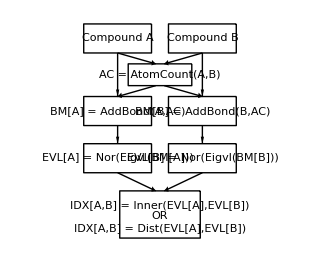

```mathematica
Graphics[{tA,bA,tB,bB(*,tA2,bA2,tB2,bB2*),mc,bmc,bA3,bB3,tA3,tB3,bA4,bB4,tA4,tB4,bidx,tidx,ar}]
```